```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/ETHUSD_BTCUSD_25SEP20/";
```

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_Tiingo_LTC/";*)
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=Module[{v},
v=Catch[CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x], _SystemException];
If[NumberQ[v],v,0]
]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
(*Print["[calibrate] α, β: " <> ToString[{α,β}]];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];
target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
(*data[[1;;10]]*)
```

( | Date | PX_LAST | contract_name | BTC Price | log return future | log return bitcoin
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 40143.7 | 0.0212907 | 0.018658
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 39401.7 | -0.0904653 | -0.0934764
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 43262.4 | -0.0196938 | -0.0216123
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 44207.6 | -0.131645 | -0.126287
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 50158.3 | 0.03685 | 0.0328265
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 48538.5 | -0.119603 | -0.11567
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 54490.5 | -0.042369 | -0.0388241
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 56647.7 | 0.018947 | 0.0163419
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 55729.5 | -0.0359909 | -0.0331504)

```mathematica
data[[1;;10]]
```

( | datetime | spot | futures | rs | rf
0 | 2020-06-17 01:00:00 | 234.03 | 9568.25 | -0.00558196 | -0.00484805
1 | 2020-06-17 02:00:00 | 232.7 | 9542.25 | -0.00569924 | -0.00272102
2 | 2020-06-17 03:00:00 | 232.46 | 9530.25 | -0.0010319 | -0.00125836
3 | 2020-06-17 04:00:00 | 232.85 | 9549.5 | 0.0016763 | 0.00201785
4 | 2020-06-17 05:00:00 | 233.09 | 9550.5 | 0.00103018 | 0.000104712
5 | 2020-06-17 06:00:00 | 232.6 | 9523.75 | -0.0021044 | -0.00280483
6 | 2020-06-17 07:00:00 | 234.3 | 9572.75 | 0.00728211 | 0.00513184
7 | 2020-06-17 08:00:00 | 234.7 | 9613.5 | 0.00170576 | 0.00424784
8 | 2020-06-17 09:00:00 | 233.99 | 9588.25 | -0.00302972 | -0.00262997)

```mathematica
data[[1,5]]
```

rs

```mathematica
data[[1,6]]
```

rf

```mathematica
α0=0.5; β0=0;
```

```mathematica
For[kk=89, kk≥0, kk--,
Print[kk];
SeedRandom[123456];
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,5⟧;
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,{6,5}⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

89

88

87

86

85

84

83

82

81

80

79

78

77

76

75

74

73

72

71

70

69

68

67

66

65

64

63

62

61

60

59

58

57

56

55

54

53

52

51

50

49

48

47

46

45

44

43

42

41

40

39

38

37

36

35

34

33

32

31

30

29

28

27

26

25

24

23

22

21

20

19

18

17

16

15

14

13

12

11

10

9

8

7

6

5

4

3

2

1

0

```mathematica
{α0,β0}
```

{1.04598,-0.123331}

```mathematica
dataDirectory
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../processed_data/ETHUSD_BTCUSD_25SEP20/

```mathematica
For[kk=0, kk≤185, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,5⟧;
(*dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;*)
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,6⟧;
rf=data2⟦2;;All,5⟧;
(*rs=data2⟦2;;All,7⟧;
rf=data2⟦2;;All,6⟧;*)
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

1

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

2

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

3

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

4

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

5

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

6

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

7

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

8

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

9

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

10

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

11

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

12

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

13

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

14

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

15

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

16

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

17

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

18

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

19

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

20

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

21

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

22

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

23

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

24

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

25

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

26

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

27

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

28

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

29

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

30

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

31

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

32

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

33

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

34

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

35

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

36

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

37

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

38

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

39

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

40

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

41

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

42

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

43

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

44

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

45

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

46

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

47

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

48

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

49

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

50

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

51

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

52

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

53

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

54

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

55

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

56

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

57

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

58

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

59

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

60

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

61

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

62

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

63

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

64

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

65

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

66

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

67

Risk Measures...

Variance

VaR 99

VaR 95

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ES 99

ES 95

Spectral 10

68

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

69

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

70

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

71

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

72

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

73

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

74

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

75

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

76

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

77

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

78

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

79

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

80

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

81

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

82

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

83

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

84

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

85

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

86

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

87

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

88

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

89

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

90

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

91

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

92

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

93

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

94

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

95

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

96

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

97

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

98

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

99

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

100

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

101

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

102

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

103

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

104

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

105

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

106

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

107

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

108

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

109

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

110

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

111

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

112

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

113

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

114

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

115

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

116

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

117

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

118

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

119

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

120

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

121

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

122

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

123

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

124

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

125

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

126

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

127

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

128

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

129

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

130

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

131

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

132

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

133

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

134

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

135

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

136

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

137

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

138

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

139

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

140

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

141

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

142

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

143

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

144

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

145

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

146

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

147

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

148

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

149

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

150

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

151

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

152

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

153

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

154

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

155

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

156

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

157

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

158

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

159

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

160

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

161

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

162

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

163

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

164

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

165

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

166

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

167

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

168

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

169

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

170

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

171

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

172

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

173

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

174

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

175

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

176

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

177

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

178

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

179

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

180

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

181

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

182

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

183

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

184

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

185

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2020-06-17-01-00-00 | 0.618562 | 0.441643 | 0.431515 | 0.397491 | 0.420596 | 0.403015
 | 2020-06-17-05-00-00 | 0.61148 | 0.438344 | 0.436446 | 0.397152 | 0.423576 | 0.387588
 | 2020-06-17-09-00-00 | 0.611619 | 0.431437 | 0.438796 | 0.394806 | 0.423376 | 0.3903
 | 2020-06-17-13-00-00 | 0.61156 | 0.433355 | 0.442176 | 0.394229 | 0.423371 | 0.3838
 | 2020-06-17-17-00-00 | 0.592945 | 0.419482 | 0.420857 | 0.391762 | 0.409716 | 0.369083
 | 2020-06-17-21-00-00 | 0.597415 | 0.42949 | 0.422482 | 0.383659 | 0.413848 | 0.377683
 | 2020-06-18-01-00-00 | 0.586215 | 0.418387 | 0.413166 | 0.38315 | 0.407035 | 0.362224
 | 2020-06-18-05-00-00 | 0.585432 | 0.419122 | 0.411778 | 0.38324 | 0.406437 | 0.361177
 | 2020-06-18-09-00-00 | 0.582573 | 0.411976 | 0.412954 | 0.379473 | 0.402669 | 0.361548
 | 2020-06-18-13-00-00 | 0.598322 | 0.424598 | 0.418075 | 0.392406 | 0.412511 | 0.372647
 | 2020-06-18-17-00-00 | 0.609383 | 0.41297 | 0.477144 | 0.388151 | 0.427586 | 0.380205
 | 2020-06-18-21-00-00 | 0.572402 | 0.380725 | 0.451737 | 0.371313 | 0.404879 | 0.335585
 | 2020-06-19-01-00-00 | 0.583611 | 0.395872 | 0.414255 | 0.369716 | 0.413739 | 0.350946
 | 2020-06-19-05-00-00 | 0.576212 | 0.388816 | 0.38867 | 0.368545 | 0.403372 | 0.35173
 | 2020-06-19-09-00-00 | 0.58779 | 0.392123 | 0.387422 | 0.366746 | 0.409481 | 0.371093
 | 2020-06-19-13-00-00 | 0.577446 | 0.395089 | 0.395662 | 0.362309 | 0.411985 | 0.35222
 | 2020-06-19-17-00-00 | 0.562632 | 0.380825 | 0.382396 | 0.354475 | 0.399207 | 0.338004
 | 2020-06-19-21-00-00 | 0.549253 | 0.36294 | 0.370558 | 0.352907 | 0.390456 | 0.327002
 | 2020-06-20-01-00-00 | 0.573014 | 0.391431 | 0.380773 | 0.355665 | 0.401881 | 0.358175
 | 2020-06-20-05-00-00 | 0.572558 | 0.391091 | 0.381961 | 0.355773 | 0.401684 | 0.356482
 | 2020-06-20-09-00-00 | 0.561496 | 0.37515 | 0.378757 | 0.35377 | 0.396133 | 0.340507
 | 2020-06-20-13-00-00 | 0.548243 | 0.362892 | 0.369527 | 0.354043 | 0.390918 | 0.324245
 | 2020-06-20-17-00-00 | 0.547657 | 0.362841 | 0.369958 | 0.353039 | 0.390837 | 0.324431
 | 2020-06-20-21-00-00 | 0.54392 | 0.354624 | 0.363991 | 0.347024 | 0.382609 | 0.310861
 | 2020-06-21-01-00-00 | 0.563657 | 0.375668 | 0.375008 | 0.352037 | 0.394562 | 0.333822
 | 2020-06-21-05-00-00 | 0.553362 | 0.355938 | 0.369513 | 0.34432 | 0.385117 | 0.325999
 | 2020-06-21-09-00-00 | 0.560239 | 0.373736 | 0.370805 | 0.350315 | 0.392214 | 0.327148
 | 2020-06-21-13-00-00 | 0.549378 | 0.354874 | 0.356813 | 0.341837 | 0.375504 | 0.328155
 | 2020-06-21-17-00-00 | 0.548469 | 0.355365 | 0.355329 | 0.341193 | 0.374901 | 0.326615
 | 2020-06-21-21-00-00 | 0.547536 | 0.352764 | 0.362196 | 0.338887 | 0.37585 | 0.326679
 | 2020-06-22-01-00-00 | 0.544183 | 0.339153 | 0.344059 | 0.337797 | 0.368582 | 0.32779
 | 2020-06-22-05-00-00 | 0.537857 | 0.348735 | 0.367155 | 0.333158 | 0.376456 | 0.303604
 | 2020-06-22-09-00-00 | 0.548895 | 0.333799 | 0.347923 | 0.338121 | 0.367498 | 0.329862
 | 2020-06-22-13-00-00 | 0.543551 | 0.345458 | 0.352232 | 0.339325 | 0.374103 | 0.312231
 | 2020-06-22-17-00-00 | 0.539397 | 0.337111 | 0.346514 | 0.337905 | 0.369175 | 0.325417
 | 2020-06-22-21-00-00 | 0.539958 | 0.355752 | 0.358607 | 0.345192 | 0.37895 | 0.313342
 | 2020-06-23-01-00-00 | 0.570704 | 0.376657 | 0.390962 | 0.361645 | 0.402301 | 0.342069
 | 2020-06-23-05-00-00 | 0.553187 | 0.355628 | 0.366554 | 0.370283 | 0.388916 | 0.318606
 | 2020-06-23-09-00-00 | 0.553792 | 0.363134 | 0.356962 | 0.370483 | 0.387996 | 0.320258
 | 2020-06-23-13-00-00 | 0.551371 | 0.353464 | 0.417937 | 0.368802 | 0.387978 | 0.318112
 | 2020-06-23-17-00-00 | 0.56101 | 0.365364 | 0.42229 | 0.364923 | 0.393433 | 0.333291
 | 2020-06-23-21-00-00 | 0.553691 | 0.357479 | 0.421408 | 0.370814 | 0.389701 | 0.314784
 | 2020-06-24-01-00-00 | 0.561665 | 0.35708 | 0.417734 | 0.360699 | 0.386513 | 0.343737
 | 2020-06-24-05-00-00 | 0.549379 | 0.35807 | 0.416687 | 0.371262 | 0.387723 | 0.317943
 | 2020-06-24-09-00-00 | 0.546465 | 0.374189 | 0.419879 | 0.352908 | 0.370507 | 0.332507
 | 2020-06-24-13-00-00 | 0.567023 | 0.320324 | 0.362943 | 0.353791 | 0.367015 | 0.366528
 | 2020-06-24-17-00-00 | 0.549522 | 0.239739 | 0.365117 | 0.317081 | 0.338946 | 0.348773
 | 2020-06-24-21-00-00 | 0.557534 | 0.235456 | 0.366518 | 0.329234 | 0.33879 | 0.359507
 | 2020-06-25-01-00-00 | 0.53715 | 0.224101 | 0.333888 | 0.32725 | 0.328965 | 0.341561
 | 2020-06-25-05-00-00 | 0.537851 | 0.251513 | 0.340517 | 0.287296 | 0.314012 | 0.354313
 | 2020-06-25-09-00-00 | 0.534274 | 0.25249 | 0.335181 | 0.280911 | 0.307338 | 0.355237
 | 2020-06-25-13-00-00 | 0.534448 | 0.261495 | 0.344614 | 0.298396 | 0.322828 | 0.340744
 | 2020-06-25-17-00-00 | 0.531605 | 0.251292 | 0.335722 | 0.291889 | 0.33017 | 0.32966
 | 2020-06-25-21-00-00 | 0.554488 | 0.249433 | 0.344573 | 0.293278 | 0.335229 | 0.353384
 | 2020-06-26-01-00-00 | 0.549815 | 0.246137 | 0.346803 | 0.292848 | 0.334122 | 0.345633
 | 2020-06-26-05-00-00 | 0.550901 | 0.247394 | 0.360155 | 0.287488 | 0.340607 | 0.34208
 | 2020-06-26-09-00-00 | 0.541143 | 0.268489 | 0.338879 | 0.280324 | 0.333369 | 0.34029
 | 2020-06-26-13-00-00 | 0.540443 | 0.272177 | 0.345947 | 0.281825 | 0.336013 | 0.340156
 | 2020-06-26-17-00-00 | 0.5286 | 0.26203 | 0.329883 | 0.273511 | 0.32324 | 0.340017
 | 2020-06-26-21-00-00 | 0.533199 | 0.264169 | 0.330893 | 0.282816 | 0.32722 | 0.341565
 | 2020-06-27-01-00-00 | 0.544482 | 0.270672 | 0.336455 | 0.287489 | 0.330803 | 0.354015
 | 2020-06-27-05-00-00 | 0.546402 | 0.271016 | 0.337425 | 0.292483 | 0.332265 | 0.353797
 | 2020-06-27-09-00-00 | 0.547528 | 0.265676 | 0.336004 | 0.290451 | 0.330663 | 0.357805
 | 2020-06-27-13-00-00 | 0.550368 | 0.271947 | 0.364203 | 0.296245 | 0.334787 | 0.355299
 | 2020-06-27-17-00-00 | 0.545076 | 0.272177 | 0.37455 | 0.287171 | 0.335275 | 0.350553
 | 2020-06-27-21-00-00 | 0.552264 | 0.29183 | 0.358097 | 0.215233 | 0.320855 | 0.376725
 | 2020-06-28-01-00-00 | 0.554192 | 0.317097 | 0.391501 | 0.220312 | 0.330087 | 0.373077
 | 2020-06-28-05-00-00 | 0.545152 | 0.319697 | 0.390443 | 0.215895 | 0.32796 | 0.366332
 | 2020-06-28-09-00-00 | 0.545419 | 0.319697 | 0.39368 | 0.217646 | 0.329467 | 0.362462
 | 2020-06-28-13-00-00 | 0.548612 | 0.311436 | 0.405676 | 0.210736 | 0.332406 | 0.367292
 | 2020-06-28-17-00-00 | 0.55597 | 0.328327 | 0.395867 | 0.210354 | 0.345722 | 0.360282
 | 2020-06-28-21-00-00 | 0.556498 | 0.348869 | 0.424513 | 0.222583 | 0.350111 | 0.360769
 | 2020-06-29-01-00-00 | 0.521522 | 0.340428 | 0.413995 | 0.219712 | 0.338957 | 0.31244
 | 2020-06-29-05-00-00 | 0.536046 | 0.335669 | 0.423189 | 0.219954 | 0.345181 | 0.321148
 | 2020-06-29-09-00-00 | 0.524602 | 0.350624 | 0.388983 | 0.224586 | 0.3436 | 0.305675
 | 2020-06-29-13-00-00 | 0.547968 | 0.357864 | 0.416967 | 0.22645 | 0.356331 | 0.328465
 | 2020-06-29-17-00-00 | 0.53125 | 0.349169 | 0.376953 | 0.225858 | 0.338694 | 0.313608
 | 2020-06-29-21-00-00 | 0.565306 | 0.339712 | 0.434441 | 0.216997 | 0.360268 | 0.363473
 | 2020-06-30-01-00-00 | 0.539581 | 0.339081 | 0.431887 | 0.203803 | 0.352627 | 0.335064
 | 2020-06-30-05-00-00 | 0.540025 | 0.338681 | 0.432377 | 0.204377 | 0.353117 | 0.334936
 | 2020-06-30-09-00-00 | 0.551995 | 0.334156 | 0.438105 | 0.204444 | 0.346498 | 0.363412
 | 2020-06-30-13-00-00 | 0.526909 | 0.327828 | 0.4139 | 0.207398 | 0.344337 | 0.321198
 | 2020-06-30-17-00-00 | 0.550485 | 0.362421 | 0.414594 | 0.230622 | 0.354995 | 0.346095
 | 2020-06-30-21-00-00 | 0.56131 | 0.353717 | 0.408511 | 0.226867 | 0.348962 | 0.364582
 | 2020-07-01-01-00-00 | 0.534741 | 0.355239 | 0.415288 | 0.225435 | 0.34904 | 0.330256
 | 2020-07-01-05-00-00 | 0.528747 | 0.349477 | 0.404181 | 0.220108 | 0.344542 | 0.327143
 | 2020-07-01-09-00-00 | 0.551916 | 0.342192 | 0.402436 | 0.216137 | 0.338457 | 0.365571
 | 2020-07-01-13-00-00 | 0.51951 | 0.345007 | 0.402584 | 0.21864 | 0.339458 | 0.318013
 | 2020-07-01-17-00-00 | 0.549114 | 0.356541 | 0.442282 | 0.217194 | 0.340236 | 0.358969
 | 2020-07-01-21-00-00 | 0.541686 | 0.343093 | 0.470384 | 0.208297 | 0.340689 | 0.351652
 | 2020-07-02-01-00-00 | 0.551952 | 0.353179 | 0.449873 | 0.219528 | 0.342656 | 0.33532
 | 2020-07-02-05-00-00 | 0.553445 | 0.357663 | 0.443301 | 0.218456 | 0.341085 | 0.339299
 | 2020-07-02-09-00-00 | 0.559667 | 0.347482 | 0.466121 | 0.214941 | 0.363253 | 0.330945
 | 2020-07-02-13-00-00 | 0.561265 | 0.344067 | 0.442933 | 0.210099 | 0.352789 | 0.335031
 | 2020-07-02-17-00-00 | 0.558149 | 0.341741 | 0.426436 | 0.189769 | 0.334089 | 0.371618
 | 2020-07-02-21-00-00 | 0.573561 | 0.362583 | 0.464242 | 0.194134 | 0.349691 | 0.389132
 | 2020-07-03-01-00-00 | 0.555351 | 0.336584 | 0.466745 | 0.17858 | 0.340095 | 0.369823
 | 2020-07-03-05-00-00 | 0.558964 | 0.346005 | 0.468992 | 0.182895 | 0.344281 | 0.369973
 | 2020-07-03-09-00-00 | 0.549077 | 0.33637 | 0.458569 | 0.177991 | 0.336118 | 0.363571
 | 2020-07-03-13-00-00 | 0.547297 | 0.335593 | 0.456477 | 0.177222 | 0.334552 | 0.36401
 | 2020-07-03-17-00-00 | 0.550457 | 0.34034 | 0.456663 | 0.177235 | 0.336097 | 0.36515
 | 2020-07-03-21-00-00 | 0.553333 | 0.34168 | 0.459142 | 0.179445 | 0.337988 | 0.369562
 | 2020-07-04-01-00-00 | 0.54536 | 0.337765 | 0.453864 | 0.175033 | 0.332378 | 0.363567
 | 2020-07-04-05-00-00 | 0.540344 | 0.33199 | 0.451364 | 0.174098 | 0.328955 | 0.358612
 | 2020-07-04-09-00-00 | 0.541853 | 0.330754 | 0.453831 | 0.174213 | 0.329759 | 0.360564
 | 2020-07-04-13-00-00 | 0.541076 | 0.329922 | 0.448674 | 0.173676 | 0.328627 | 0.360093
 | 2020-07-04-17-00-00 | 0.539987 | 0.328579 | 0.452955 | 0.170744 | 0.328228 | 0.360026
 | 2020-07-04-21-00-00 | 0.531453 | 0.337882 | 0.445784 | 0.176794 | 0.3348 | 0.341505
 | 2020-07-05-01-00-00 | 0.531774 | 0.338077 | 0.44554 | 0.176863 | 0.335159 | 0.34121
 | 2020-07-05-05-00-00 | 0.537809 | 0.350567 | 0.455914 | 0.177552 | 0.34173 | 0.344423
 | 2020-07-05-09-00-00 | 0.535937 | 0.34798 | 0.449187 | 0.17471 | 0.337162 | 0.348708
 | 2020-07-05-13-00-00 | 0.550067 | 0.378698 | 0.461788 | 0.190812 | 0.345672 | 0.358874
 | 2020-07-05-17-00-00 | 0.54858 | 0.376884 | 0.461084 | 0.190023 | 0.344765 | 0.358466
 | 2020-07-05-21-00-00 | 0.551561 | 0.379078 | 0.459933 | 0.191094 | 0.346304 | 0.361907
 | 2020-07-06-01-00-00 | 0.550779 | 0.379078 | 0.464698 | 0.191119 | 0.34812 | 0.356564
 | 2020-07-06-05-00-00 | 0.545537 | 0.37213 | 0.45728 | 0.190367 | 0.342668 | 0.35392
 | 2020-07-06-09-00-00 | 0.53959 | 0.383905 | 0.466448 | 0.190916 | 0.35432 | 0.347911
 | 2020-07-06-13-00-00 | 0.540544 | 0.375662 | 0.452044 | 0.192553 | 0.347154 | 0.329053
 | 2020-07-06-17-00-00 | 0.533835 | 0.376262 | 0.469485 | 0.194064 | 0.351768 | 0.323069
 | 2020-07-06-21-00-00 | 0.536246 | 0.368453 | 0.44601 | 0.183969 | 0.349094 | 0.328221
 | 2020-07-07-01-00-00 | 0.529628 | 0.359796 | 0.476201 | 0.178379 | 0.359751 | 0.312595
 | 2020-07-07-05-00-00 | 0.521052 | 0.360402 | 0.449046 | 0.172477 | 0.345111 | 0.320228
 | 2020-07-07-09-00-00 | 0.525112 | 0.338324 | 0.457394 | 0.175959 | 0.337338 | 0.336458
 | 2020-07-07-13-00-00 | 0.518775 | 0.351492 | 0.346606 | 0.176887 | 0.33339 | 0.325101
 | 2020-07-07-17-00-00 | 0.517662 | 0.348103 | 0.312834 | 0.171895 | 0.323064 | 0.332555
 | 2020-07-07-21-00-00 | 0.514659 | 0.342221 | 0.311403 | 0.173063 | 0.322431 | 0.330084
 | 2020-07-08-01-00-00 | 0.501494 | 0.336275 | 0.29084 | 0.159266 | 0.309726 | 0.322925
 | 2020-07-08-05-00-00 | 0.492519 | 0.323896 | 0.296458 | 0.160068 | 0.30803 | 0.312762
 | 2020-07-08-09-00-00 | 0.496349 | 0.351063 | 0.305612 | 0.171724 | 0.302414 | 0.313614
 | 2020-07-08-13-00-00 | 0.500634 | 0.349484 | 0.304025 | 0.16719 | 0.301891 | 0.320857
 | 2020-07-08-17-00-00 | 0.504259 | 0.382225 | 0.324346 | 0.187718 | 0.333032 | 0.273
 | 2020-07-08-21-00-00 | 0.501109 | 0.382461 | 0.310525 | 0.181008 | 0.326845 | 0.271647
 | 2020-07-09-01-00-00 | 0.454592 | 0.391182 | 0.312515 | 0.188001 | 0.308491 | 0.287474
 | 2020-07-09-05-00-00 | 0.442044 | 0.369531 | 0.317614 | 0.177145 | 0.301759 | 0.269477
 | 2020-07-09-09-00-00 | 0.437094 | 0.359817 | 0.328739 | 0.172335 | 0.294677 | 0.257859
 | 2020-07-09-13-00-00 | 0.438461 | 0.357633 | 0.330445 | 0.171102 | 0.2963 | 0.263154
 | 2020-07-09-17-00-00 | 0.436958 | 0.380092 | 0.291875 | 0.186298 | 0.253552 | 0.263031
 | 2020-07-09-21-00-00 | 0.436539 | 0.346135 | 0.240187 | 0.165008 | 0.2466 | 0.26042
 | 2020-07-10-01-00-00 | 0.386942 | 0.298176 | 0.279571 | 0.163633 | 0.229353 | 0.234385
 | 2020-07-10-05-00-00 | 0.439308 | 0.343275 | 0.228547 | 0.165499 | 0.243717 | 0.259653
 | 2020-07-10-09-00-00 | 0.376157 | 0.29503 | 0.255406 | 0.197244 | 0.231924 | 0.239745
 | 2020-07-10-13-00-00 | 0.412291 | 0.312231 | 0.267858 | 0.196659 | 0.247491 | 0.262107
 | 2020-07-10-17-00-00 | 0.398442 | 0.288444 | 0.256478 | 0.206008 | 0.250069 | 0.265552
 | 2020-07-10-21-00-00 | 0.413281 | 0.335977 | 0.278806 | 0.185658 | 0.251006 | 0.25727
 | 2020-07-11-01-00-00 | 0.397938 | 0.298898 | 0.268488 | 0.184078 | 0.249197 | 0.243022
 | 2020-07-11-05-00-00 | 0.409361 | 0.324017 | 0.271425 | 0.185845 | 0.254972 | 0.253649
 | 2020-07-11-09-00-00 | 0.392408 | 0.292447 | 0.257166 | 0.187249 | 0.248487 | 0.240752
 | 2020-07-11-13-00-00 | 0.363451 | 0.279642 | 0.220296 | 0.185693 | 0.227563 | 0.235166
 | 2020-07-11-17-00-00 | 0.351947 | 0.285765 | 0.219926 | 0.19403 | 0.231554 | 0.232838
 | 2020-07-11-21-00-00 | 0.442682 | 0.30191 | 0.231858 | 0.196201 | 0.251161 | 0.286762
 | 2020-07-12-01-00-00 | 0.421451 | 0.309784 | 0.256544 | 0.202843 | 0.255141 | 0.334175
 | 2020-07-12-05-00-00 | 0.467713 | 0.323141 | 0.283214 | 0.208955 | 0.281719 | 0.360718
 | 2020-07-12-09-00-00 | 0.474288 | 0.327788 | 0.285142 | 0.210892 | 0.285868 | 0.316869
 | 2020-07-12-13-00-00 | 0.422434 | 0.240934 | 0.271383 | 0.169865 | 0.216438 | 0.311726
 | 2020-07-12-17-00-00 | 0.429274 | 0.289756 | 0.273092 | 0.173495 | 0.223183 | 0.312459
 | 2020-07-12-21-00-00 | 0.437998 | 0.281634 | 0.276886 | 0.158295 | 0.235831 | 0.306785
 | 2020-07-13-01-00-00 | 0.435346 | 0.272431 | 0.277677 | 0.164464 | 0.240408 | 0.306577
 | 2020-07-13-05-00-00 | 0.437147 | 0.247624 | 0.247524 | 0.154764 | 0.20371 | 0.342661
 | 2020-07-13-09-00-00 | 0.451111 | 0.255785 | 0.256866 | 0.146423 | 0.200696 | 0.344612
 | 2020-07-13-13-00-00 | 0.416391 | 0.238927 | 0.222052 | 0.136865 | 0.183722 | 0.317653
 | 2020-07-13-17-00-00 | 0.377096 | 0.217368 | 0.192116 | 0.12266 | 0.187732 | 0.280689
 | 2020-07-13-21-00-00 | 0.367333 | 0.186487 | 0.136493 | 0.0812512 | 0.12637 | 0.340079
 | 2020-07-14-01-00-00 | 0.375153 | 0.156928 | 0.0737361 | 0.0871337 | 0.137628 | 0.341721
 | 2020-07-14-05-00-00 | 0.323669 | 0.117337 | 0.0933738 | 0.0739461 | 0.138734 | 0.292536
 | 2020-07-14-09-00-00 | 0.327915 | 0.120794 | 0.045413 | 0.0760122 | 0.159149 | 0.287625
 | 2020-07-14-13-00-00 | 0.383855 | 0.128008 | 0.185544 | 0.0795281 | 0.175146 | 0.329786
 | 2020-07-14-17-00-00 | 0.391293 | 0.117395 | 0.170292 | 0.0812043 | 0.161571 | 0.32406
 | 2020-07-14-21-00-00 | 0.389326 | 0.105533 | 0.264533 | 0.083033 | 0.187732 | 0.298084
 | 2020-07-15-01-00-00 | 0.375397 | 0.0888107 | 0.246131 | 0.0786459 | 0.174188 | 0.288667
 | 2020-07-15-05-00-00 | 0.38306 | 0.0927177 | 0.238321 | 0.0788422 | 0.175567 | 0.300975
 | 2020-07-15-09-00-00 | 0.38899 | 0.0977796 | 0.258442 | 0.0836946 | 0.184146 | 0.326861
 | 2020-07-15-13-00-00 | 0.389116 | 0.0938878 | 0.312517 | 0.0801844 | 0.184693 | 0.327087
 | 2020-07-15-17-00-00 | 0.367169 | 0.0768335 | 0.287498 | 0.0714846 | 0.167478 | 0.316661
 | 2020-07-15-21-00-00 | 0.372574 | 0.0822481 | 0.291394 | 0.0719522 | 0.169732 | 0.321516
 | 2020-07-16-01-00-00 | 0.384704 | 0.099639 | 0.289605 | 0.0801679 | 0.185418 | 0.313759
 | 2020-07-16-05-00-00 | 0.388949 | 0.106248 | 0.273901 | 0.0816822 | 0.182672 | 0.316294
 | 2020-07-16-09-00-00 | 0.391537 | 0.111065 | 0.242166 | 0.084592 | 0.189582 | 0.317974
 | 2020-07-16-13-00-00 | 0.386306 | 0.107414 | 0.236137 | 0.0811917 | 0.189136 | 0.312555
 | 2020-07-16-17-00-00 | 0.38409 | 0.124324 | 0.254611 | 0.081734 | 0.199934 | 0.30613
 | 2020-07-16-21-00-00 | 0.387107 | 0.118466 | 0.253349 | 0.0787535 | 0.203022 | 0.302348
 | 2020-07-17-01-00-00 | 0.353856 | 0.112784 | 0.239365 | 0.0795244 | 0.201112 | 0.27306
 | 2020-07-17-05-00-00 | 0.354186 | 0.114695 | 0.236883 | 0.0797372 | 0.20074 | 0.272228
 | 2020-07-17-09-00-00 | 0.351972 | 0.129842 | 0.237156 | 0.0844421 | 0.205391 | 0.276014
 | 2020-07-17-13-00-00 | 0.381272 | 0.135347 | 0.243262 | 0.0929199 | 0.208035 | 0.303392
 | 2020-07-17-17-00-00 | 0.405136 | 0.12904 | 0.23926 | 0.0902014 | 0.209604 | 0.317475
 | 2020-07-17-21-00-00 | 0.345617 | 0.135594 | 0.222939 | 0.0945725 | 0.203179 | 0.273743

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2020-06-17-01-00-00 | 0.865535 | 0.45568 | 0.600005 | 0.533404 | 0.581253 | 0.629657
 | 2020-06-17-05-00-00 | 0.187463 | -0.973139 | -0.590345 | -0.933534 | -0.736774 | 0.443091
 | 2020-06-17-09-00-00 | -1.16996 | -4.34576 | -3.84604 | -4.15262 | -3.72484 | 0.943534
 | 2020-06-17-13-00-00 | 0.765882 | 2.67985 | 1.77855 | 2.47468 | 1.77855 | 0.575833
 | 2020-06-17-17-00-00 | -1.20004 | -1.22817 | -0.765472 | -1.14575 | -0.897343 | 0.0920791
 | 2020-06-17-21-00-00 | -1.82001 | -0.36875 | -0.335187 | -0.361166 | -0.334415 | 64.479
 | 2020-06-18-01-00-00 | -0.122832 | -0.884011 | -0.608597 | -0.817719 | -0.524166 | -0.0522513
 | 2020-06-18-05-00-00 | -48.8218 | 0.216039 | 0.266178 | 0.227049 | 0.288149 | -3057.63
 | 2020-06-18-09-00-00 | 0.593403 | 0.491853 | 0.538411 | 0.501603 | 0.558362 | -0.23857
 | 2020-06-18-13-00-00 | 0.940273 | 0.763255 | 0.796699 | 0.783853 | 0.801359 | 0.56419
 | 2020-06-18-17-00-00 | -0.96778 | -0.938051 | -0.840501 | -0.869461 | -0.873004 | -0.120119
 | 2020-06-18-21-00-00 | 0.965694 | 0.581753 | 0.794661 | 0.621001 | 0.816346 | 0.64459
 | 2020-06-19-01-00-00 | -5.02292 | -3.4541 | -2.70592 | -3.33509 | -3.03354 | -0.937404
 | 2020-06-19-05-00-00 | -1.81007 | -2.64215 | -2.08314 | -2.61597 | -2.38143 | 0.0127653
 | 2020-06-19-09-00-00 | 0.532236 | 0.201195 | 0.4203 | 0.345383 | 0.392848 | 0.46843
 | 2020-06-19-13-00-00 | 0.671355 | 0.869241 | 0.836303 | 0.848603 | 0.805037 | 0.150689
 | 2020-06-19-17-00-00 | -0.0701313 | 0.217956 | 0.187373 | 0.214253 | 0.206273 | -1.35176
 | 2020-06-19-21-00-00 | -2.27911 | 0.397483 | 0.597328 | 0.43072 | 0.489756 | -3.68403
 | 2020-06-20-01-00-00 | -1.56616 | -9.86942 | -6.9946 | -9.68877 | -9.10689 | 0.369067
 | 2020-06-20-05-00-00 | -1.72195 | -0.868522 | -0.584559 | -0.849155 | -0.792146 | -0.33594
 | 2020-06-20-09-00-00 | 0.772322 | 0.56309 | 0.46328 | 0.545033 | 0.518731 | 0.352404
 | 2020-06-20-13-00-00 | 0.293865 | -0.0893856 | -0.0743132 | -0.0886151 | -0.0835103 | 0.286914
 | 2020-06-20-17-00-00 | 0.647675 | -1.9042 | -0.753433 | -1.84114 | -1.45408 | 0.774569
 | 2020-06-20-21-00-00 | -0.647497 | -1.49636 | -0.80918 | -1.45066 | -1.2357 | 0.00235021
 | 2020-06-21-01-00-00 | -27.0883 | -1.10903 | -0.941066 | -1.06126 | -0.959948 | -20.4043
 | 2020-06-21-05-00-00 | 0.942348 | 0.824485 | 0.825879 | 0.825134 | 0.825499 | 0.126467
 | 2020-06-21-09-00-00 | -11.1521 | -1.07017 | -0.992167 | -1.04402 | -0.992496 | -14.4674
 | 2020-06-21-13-00-00 | -3.19776 | -0.890694 | -0.660106 | -0.753009 | -0.77293 | -1.36394
 | 2020-06-21-17-00-00 | 0.846428 | 0.262979 | 0.285743 | 0.276428 | 0.275032 | 0.837325
 | 2020-06-21-21-00-00 | 0.470506 | -6.12297 | -4.99953 | -5.37971 | -5.28798 | 0.911817
 | 2020-06-22-01-00-00 | -0.49563 | -1.25119 | -0.836223 | -1.05189 | -1.06889 | 0.263118
 | 2020-06-22-05-00-00 | 0.92772 | -2.48384 | -1.17538 | -1.50409 | -1.26585 | 0.973098
 | 2020-06-22-09-00-00 | 0.160728 | -3.69886 | -2.78846 | -3.07443 | -3.19799 | 1.00623
 | 2020-06-22-13-00-00 | -0.20365 | -5.11014 | -4.42296 | -5.00458 | -4.71801 | 0.430757
 | 2020-06-22-17-00-00 | -0.286504 | -0.313269 | -0.210335 | -0.245619 | -0.20044 | 0.180269
 | 2020-06-22-21-00-00 | 0.944772 | -1.25681 | -0.83054 | -1.19912 | -0.833921 | 1.10275
 | 2020-06-23-01-00-00 | 0.140714 | 0.537335 | 0.509528 | 0.533786 | 0.530182 | -0.657764
 | 2020-06-23-05-00-00 | -38.9093 | -0.41117 | -0.271111 | -0.37895 | -0.341015 | 11.8119
 | 2020-06-23-09-00-00 | -0.270515 | 0.0467097 | 0.340002 | 0.132388 | 0.22029 | -0.444562
 | 2020-06-23-13-00-00 | -3.48333 | -5.46004 | -4.03497 | -5.13727 | -4.77042 | 0.650897
 | 2020-06-23-17-00-00 | -0.821914 | -0.897629 | -0.634938 | -0.813077 | -0.750968 | -0.194434
 | 2020-06-23-21-00-00 | -57.0297 | 23.191 | 18.8392 | 22.0168 | 21.0233 | -0.943998
 | 2020-06-24-01-00-00 | -1.39268 | -5.93322 | -4.06272 | -4.71528 | -4.81919 | 0.328081
 | 2020-06-24-05-00-00 | -1.84165 | 0.0680352 | 0.168874 | 0.0863066 | 0.127676 | -1.94767
 | 2020-06-24-09-00-00 | -5.40651 | -18.5878 | -12.3304 | -18.3354 | -16.8683 | 0.948089
 | 2020-06-24-13-00-00 | 0.852267 | -1.26217 | 0.255581 | -0.376437 | -0.431765 | 0.662314
 | 2020-06-24-17-00-00 | -3.13188 | -5.04324 | -3.90317 | -4.84763 | -4.02191 | 0.569185
 | 2020-06-24-21-00-00 | -3.84627 | 0.0458771 | -0.254821 | -0.471214 | -0.344538 | -1.8549
 | 2020-06-25-01-00-00 | -0.168697 | 0.653778 | 0.764577 | 0.666921 | 0.719887 | -3.28856
 | 2020-06-25-05-00-00 | -1.65477 | -4.59148 | -6.87504 | -8.78977 | -7.74807 | 0.316076
 | 2020-06-25-09-00-00 | -0.626822 | -0.270283 | -0.616111 | -0.799106 | -0.764895 | -0.0520085
 | 2020-06-25-13-00-00 | 0.766568 | 0.81653 | 0.881074 | 0.809168 | 0.838477 | -1.00785
 | 2020-06-25-17-00-00 | 0.0367162 | -1.31258 | -1.29616 | -1.52624 | -1.38241 | 0.530337
 | 2020-06-25-21-00-00 | -0.942128 | -5.66829 | -4.29845 | -5.40724 | -4.8704 | 1.24948
 | 2020-06-26-01-00-00 | -10.3054 | 0.463275 | 0.566074 | 0.478458 | 0.518129 | -22.3142
 | 2020-06-26-05-00-00 | -1.69991 | 0.464358 | 0.329906 | 0.31183 | 0.356655 | -15.9426
 | 2020-06-26-09-00-00 | -0.374985 | -0.942178 | -0.911469 | -0.864154 | -0.691909 | 0.188813
 | 2020-06-26-13-00-00 | 0.697618 | -2.04259 | -1.79665 | -1.66952 | -1.46311 | 0.898255
 | 2020-06-26-17-00-00 | 0.610749 | 0.735182 | 0.825553 | 0.822628 | 0.859282 | 0.0244238
 | 2020-06-26-21-00-00 | 0.744071 | -1.77253 | -1.46218 | -1.48977 | -1.36053 | 0.828495
 | 2020-06-27-01-00-00 | -10.2292 | -1.64202 | -1.52314 | -1.50887 | -1.49359 | -7.66355
 | 2020-06-27-05-00-00 | -1.69872 | -2.35303 | -1.95861 | -1.90577 | -1.83881 | -0.274627
 | 2020-06-27-09-00-00 | 0.540752 | 0.708554 | 0.726646 | 0.728591 | 0.73066 | 105.892
 | 2020-06-27-13-00-00 | -35.4773 | 61.1127 | 56.1604 | 56.8954 | 56.3803 | -1.62856
 | 2020-06-27-17-00-00 | -0.389658 | 1.10839 | 1.12032 | 1.12283 | 1.12644 | -5.0259
 | 2020-06-27-21-00-00 | -3.10453 | -8.83272 | -9.68739 | -7.15679 | -9.67421 | 0.447755
 | 2020-06-28-01-00-00 | -0.81105 | -10.1079 | -12.3053 | -8.17981 | -10.9631 | 0.429432
 | 2020-06-28-05-00-00 | -7.55628 | -0.32076 | -0.598868 | -0.0600014 | -0.396532 | 12.8225
 | 2020-06-28-09-00-00 | -0.496824 | 0.689231 | 0.579708 | 0.79145 | 0.653936 | -2.53208
 | 2020-06-28-13-00-00 | -1.50469 | 0.514826 | 0.258185 | 0.679719 | 0.357754 | -3.88696
 | 2020-06-28-17-00-00 | -3.54417 | -3.56278 | -4.08453 | -2.74077 | -3.98799 | -0.116198
 | 2020-06-28-21-00-00 | -4.46121 | -176.222 | -195.549 | -119.188 | -184.191 | 0.365211
 | 2020-06-29-01-00-00 | 0.0170396 | 0.392151 | 0.280787 | 0.482518 | 0.345192 | -0.361323
 | 2020-06-29-05-00-00 | -0.442357 | 0.0677228 | -0.410684 | 0.325984 | -0.212886 | -0.0662621
 | 2020-06-29-09-00-00 | -11.4104 | 7.28832 | 12.7838 | 6.53525 | 10.677 | -0.44465
 | 2020-06-29-13-00-00 | 0.425061 | 1.08399 | 1.23222 | 0.951115 | 1.2226 | -1.57538
 | 2020-06-29-17-00-00 | -0.62493 | 0.605528 | 0.545714 | 0.743062 | 0.613956 | -5.86401
 | 2020-06-29-21-00-00 | -2.90472 | -4.93943 | -6.95773 | -3.67046 | -5.70898 | 0.705768
 | 2020-06-30-01-00-00 | -2.05654 | 0.0465544 | -0.93656 | 0.353324 | -0.39787 | -1.1945
 | 2020-06-30-05-00-00 | 0.615313 | 0.620438 | 0.431456 | 0.65279 | 0.535584 | -0.685364
 | 2020-06-30-09-00-00 | 0.811362 | 0.0982101 | -0.697839 | 0.0661372 | -0.0503194 | 0.851319
 | 2020-06-30-13-00-00 | -0.847459 | -0.0981876 | -1.10587 | 0.223218 | -0.528397 | -0.713531
 | 2020-06-30-17-00-00 | -0.916858 | -7.96425 | -12.3347 | -4.10957 | -11.066 | 0.569723
 | 2020-06-30-21-00-00 | 0.609926 | 0.829774 | 0.837355 | 0.817959 | 0.836569 | -1.14756
 | 2020-07-01-01-00-00 | -9.86838 | 0.450302 | 0.191684 | 0.382772 | 0.308345 | -7.52572
 | 2020-07-01-05-00-00 | -177.876 | -4.33473 | -5.50616 | -3.2837 | -5.12761 | 11.1381
 | 2020-07-01-09-00-00 | 0.966509 | 0.999446 | 0.945333 | 0.871135 | 0.969652 | 0.693753
 | 2020-07-01-13-00-00 | 0.332151 | 0.785397 | 0.757184 | 0.734052 | 0.816157 | -1.20888
 | 2020-07-01-17-00-00 | -0.237694 | 0.408338 | 0.317681 | 0.50376 | 0.393613 | 17.251
 | 2020-07-01-21-00-00 | 0.710718 | -0.346181 | -0.59769 | -0.272012 | -0.476971 | 0.82289
 | 2020-07-02-01-00-00 | 0.236582 | 0.480299 | 0.0138164 | 0.604714 | 0.291223 | -0.0246319
 | 2020-07-02-05-00-00 | -1.3892 | 1.0824 | 1.09463 | 1.06486 | 1.08508 | -12.6259
 | 2020-07-02-09-00-00 | 0.350603 | 0.559624 | 0.335507 | 0.758589 | 0.477136 | -0.812842
 | 2020-07-02-13-00-00 | 0.212461 | -7.71923 | -11.4047 | -5.64308 | -9.20144 | 0.75679
 | 2020-07-02-17-00-00 | -7.05597 | -0.776324 | -1.83406 | -0.0764489 | -1.3291 | -2.85156
 | 2020-07-02-21-00-00 | -2.10324 | -1.4037 | -2.15783 | -1.00003 | -1.80918 | -0.0146909
 | 2020-07-03-01-00-00 | -3.2911 | -0.408271 | -1.39956 | 0.144813 | -0.868484 | -3.79477
 | 2020-07-03-05-00-00 | -5.47913 | -1.81911 | -2.7831 | -1.19559 | -2.2698 | -1.43139
 | 2020-07-03-09-00-00 | 0.527955 | 1.06715 | -1.11034 | 1.24567 | -0.0676764 | 0.349725
 | 2020-07-03-13-00-00 | 0.876305 | 0.405271 | 0.59931 | 0.295605 | 0.494452 | 0.654857
 | 2020-07-03-17-00-00 | 0.468694 | 1.04696 | -1.40041 | 1.54188 | -0.107359 | 0.262173
 | 2020-07-03-21-00-00 | -9.52819 | -1.03063 | -1.58783 | -0.690674 | -1.32097 | -4.58428
 | 2020-07-04-01-00-00 | -4.25806 | -1.09162 | -2.27114 | -0.407312 | -1.66114 | -12.8384
 | 2020-07-04-05-00-00 | -0.00882613 | 0.129123 | -0.424659 | 0.101678 | -0.109537 | 0.0950236
 | 2020-07-04-09-00-00 | -0.443856 | -3.79121 | -9.00068 | -2.57949 | -6.86397 | 0.705544
 | 2020-07-04-13-00-00 | -0.409491 | 0.160447 | -0.387513 | 0.345842 | -0.111345 | -0.441301
 | 2020-07-04-17-00-00 | 0.395903 | 0.146004 | -0.325085 | 0.0989881 | 0.0185385 | 0.592202
 | 2020-07-04-21-00-00 | -9.91591 | -1.8778 | -4.53755 | -0.571872 | -3.36886 | -2.01833
 | 2020-07-05-01-00-00 | -2.4331 | 0.388253 | -0.18808 | 0.446745 | 0.0853048 | -3.06207
 | 2020-07-05-05-00-00 | -4.69951 | -0.0279489 | -1.41298 | 0.71683 | -0.661858 | -1.84083
 | 2020-07-05-09-00-00 | -0.897222 | 0.33366 | 0.140454 | 0.518147 | 0.274773 | -57.282
 | 2020-07-05-13-00-00 | 0.846438 | 0.895604 | 0.265408 | 0.814098 | 0.654697 | 0.454237
 | 2020-07-05-17-00-00 | -0.167551 | -21.1304 | -37.9363 | -13.0896 | -28.0198 | 0.828711
 | 2020-07-05-21-00-00 | -13.3649 | 14.9875 | 23.7986 | 9.2851 | 18.9271 | 0.961151
 | 2020-07-06-01-00-00 | -0.724223 | 0.348502 | -0.01743 | 0.478735 | 0.187836 | -5.68848
 | 2020-07-06-05-00-00 | -128.057 | -5.93591 | -8.44853 | -3.53454 | -6.83238 | -18.0868
 | 2020-07-06-09-00-00 | 0.73271 | 0.851124 | 0.621529 | 0.862116 | 0.761584 | -1.09616
 | 2020-07-06-13-00-00 | -0.795103 | -0.843817 | -1.44292 | -0.190724 | -0.808772 | 0.237339
 | 2020-07-06-17-00-00 | -4.46884 | 0.344454 | 0.146454 | 0.431913 | 0.283912 | -2.48372
 | 2020-07-06-21-00-00 | -20.2149 | -15.7488 | -18.0348 | -7.54912 | -13.5421 | -0.508289
 | 2020-07-07-01-00-00 | -2.1441 | -6.98897 | -8.18782 | -2.05802 | -6.00682 | 0.617863
 | 2020-07-07-05-00-00 | 0.894171 | 129.073 | 187.018 | 34.4981 | 96.7496 | 0.919354
 | 2020-07-07-09-00-00 | 0.144633 | -2.29931 | -5.77109 | 0.246562 | -3.20476 | 0.736464
 | 2020-07-07-13-00-00 | 0.623084 | 0. | 0. | 0. | 0. | 0.370328
 | 2020-07-07-17-00-00 | 0.0510433 | -0.711057 | -1.37891 | 0.324486 | -0.680673 | 0.983393
 | 2020-07-07-21-00-00 | -16.8685 | 23.5437 | 33.4579 | 14.3429 | 25.6474 | -0.604552
 | 2020-07-08-01-00-00 | -1.69705 | 0.273968 | 0.160424 | 0.477786 | 0.240669 | -5.314
 | 2020-07-08-05-00-00 | -0.221552 | 0.753247 | 0.707226 | 0.79959 | 0.740797 | 5.99255
 | 2020-07-08-09-00-00 | 0.279736 | 3.12178 | 3.76563 | 1.22236 | 3.04716 | 1.20367
 | 2020-07-08-13-00-00 | -1.01308 | -0.709377 | -1.09017 | -0.101419 | -0.820591 | 0.525019
 | 2020-07-08-17-00-00 | -2.53276 | -3.60098 | -3.76866 | -0.495941 | -2.77934 | -0.126805
 | 2020-07-08-21-00-00 | -10.5911 | 410.744 | 440.595 | 226.556 | 380.591 | 1.14292
 | 2020-07-09-01-00-00 | -16.8716 | -0.666533 | -0.793299 | -0.339357 | -1.02292 | -5.8868
 | 2020-07-09-05-00-00 | -12.6724 | -0.453377 | -0.505912 | 0.382525 | -0.753693 | -3.38069
 | 2020-07-09-09-00-00 | -12.4912 | -4.21739 | -5.96909 | -2.19756 | -4.8202 | -0.189132
 | 2020-07-09-13-00-00 | -28.5907 | -8.80833 | -11.4834 | -4.75837 | -9.56968 | 0.715332
 | 2020-07-09-17-00-00 | -93.5715 | -9.46445 | -9.29669 | -6.82636 | -11.6739 | -4.27624
 | 2020-07-09-21-00-00 | -16.7752 | -2.58782 | -1.6486 | -0.793874 | -2.5725 | -2.34528
 | 2020-07-10-01-00-00 | -39.3141 | -1.14653 | -0.894647 | -0.545851 | -1.16593 | 39.0234
 | 2020-07-10-05-00-00 | -10.2776 | -0.275351 | -0.00476015 | 0.225549 | -0.295649 | -5.14236
 | 2020-07-10-09-00-00 | -22.3782 | -7.69673 | -5.16185 | -4.85079 | -6.28864 | -0.00988171
 | 2020-07-10-13-00-00 | -53.0932 | -10.391 | -6.74483 | -6.36515 | -8.77215 | -3.57832
 | 2020-07-10-17-00-00 | -3.20495 | -4.6953 | -3.1408 | -2.0915 | -3.38744 | 1.03543
 | 2020-07-10-21-00-00 | -9.22597 | -0.536526 | -0.0215585 | 0.0592245 | -0.464157 | -5.30517
 | 2020-07-11-01-00-00 | -41.8734 | 79.6373 | 59.9236 | 56.2427 | 87.9713 | -0.892813
 | 2020-07-11-05-00-00 | -6.77157 | -0.923605 | -0.617954 | -0.574237 | -1.02429 | -2.56437
 | 2020-07-11-09-00-00 | -0.252665 | 0.530898 | 0.552944 | 0.566959 | 0.513288 | -0.160819
 | 2020-07-11-13-00-00 | -10.7239 | -2.51058 | -1.90808 | -1.69943 | -2.91807 | -0.353524
 | 2020-07-11-17-00-00 | -6.46474 | -5.36624 | -3.83581 | -3.75715 | -6.36176 | 0.685484
 | 2020-07-11-21-00-00 | -43.9758 | -7.93805 | -5.46223 | -5.42044 | -7.93632 | -1.29199
 | 2020-07-12-01-00-00 | -27.3175 | -0.448464 | -0.285801 | -0.16298 | -0.60339 | -14.3356
 | 2020-07-12-05-00-00 | -44.4811 | -12.6784 | -14.658 | -8.8582 | -13.2999 | 1.11446
 | 2020-07-12-09-00-00 | -7.7729 | -11.44 | -10.708 | -6.86937 | -10.6747 | -1.21353
 | 2020-07-12-13-00-00 | -9.84337 | -1.01649 | -1.0645 | -0.290415 | -0.940123 | -5.75526
 | 2020-07-12-17-00-00 | -10.3932 | -0.253923 | -0.396997 | 0.0956695 | -0.377078 | -37.214
 | 2020-07-12-21-00-00 | -57.1311 | 29.5818 | 46.2131 | 17.8699 | 31.5223 | 0.153563
 | 2020-07-13-01-00-00 | -6.9264 | 70.9764 | 78.1603 | 44.8554 | 77.23 | 0.301794
 | 2020-07-13-05-00-00 | -4.43059 | -0.821881 | -1.45284 | -0.492303 | -1.0899 | -2.84411
 | 2020-07-13-09-00-00 | -1.94386 | -4.24521 | -5.2834 | -2.9358 | -4.26375 | 0.62874
 | 2020-07-13-13-00-00 | -0.725628 | 1.06965 | 1.05149 | 1.06793 | 1.07195 | -3.41366
 | 2020-07-13-17-00-00 | -0.054149 | -0.596736 | -4.24543 | -0.512322 | -1.59122 | 0.385988
 | 2020-07-13-21-00-00 | 0.319927 | 0.671591 | 0.392298 | 0.421132 | 0.734566 | -0.388105
 | 2020-07-14-01-00-00 | -0.162346 | -0.273183 | -0.161004 | -0.164997 | -0.29608 | -0.629547
 | 2020-07-14-05-00-00 | 0.908231 | 0.690728 | 0.321836 | 0.473879 | 0.864145 | -1.53846
 | 2020-07-14-09-00-00 | 0.360321 | 0.34825 | 0.55366 | 0.240872 | 0.463248 | -0.236118
 | 2020-07-14-13-00-00 | 0.430544 | 54.1657 | 128.338 | 28.0735 | 87.8844 | 0.515661
 | 2020-07-14-17-00-00 | 0.978722 | 0.665348 | 0.85476 | 0.415631 | 0.808639 | -0.0867066
 | 2020-07-14-21-00-00 | -1.22955 | 0.121665 | 0.133192 | 0.0846437 | 0.170322 | -1.7556
 | 2020-07-15-01-00-00 | 0.0190895 | 0.929173 | 0.511031 | 1.15006 | 0.759157 | -0.75402
 | 2020-07-15-05-00-00 | 0.70689 | 0.141056 | -0.516097 | 0.179496 | -0.0823371 | 0.770523
 | 2020-07-15-09-00-00 | 0.616854 | 0.565596 | 0.225862 | 0.547276 | 0.422468 | 0.227596
 | 2020-07-15-13-00-00 | -0.0843606 | -0.258116 | -0.448482 | -0.167042 | -0.339439 | 0.0800451
 | 2020-07-15-17-00-00 | 0.722629 | 0.137503 | 0.214437 | 0.0835476 | 0.165849 | 0.535708
 | 2020-07-15-21-00-00 | 0.725664 | 0.280305 | 0.698951 | 0.271263 | 0.542487 | 0.322791
 | 2020-07-16-01-00-00 | 0.0516239 | 0.282763 | 0.433243 | 0.176644 | 0.329816 | -4.56124
 | 2020-07-16-05-00-00 | 0.465346 | 0.0790485 | 0.0583048 | 0.0482256 | 0.0892005 | 1.39526
 | 2020-07-16-09-00-00 | 0.435352 | 0.315745 | 0.141747 | 0.400359 | 0.255122 | 0.221974
 | 2020-07-16-13-00-00 | 0.868562 | 0.388018 | 0.788625 | 0.323881 | 0.593495 | 0.562638
 | 2020-07-16-17-00-00 | -0.794763 | 10.1978 | 22.0224 | 6.94955 | 14.2945 | 2.40245
 | 2020-07-16-21-00-00 | -4.71524 | -0.592224 | -2.56774 | -0.192945 | -1.5696 | -0.847157
 | 2020-07-17-01-00-00 | -3.50828 | -0.00212476 | -0.0180183 | 0.00793357 | -0.0099357 | 20.2662
 | 2020-07-17-05-00-00 | 0.257205 | 0.0733764 | -3.93804 | 0.640656 | -1.82025 | 0.642142
 | 2020-07-17-09-00-00 | -0.550443 | -0.437075 | -2.09571 | 0.351985 | -1.37949 | 0.957909
 | 2020-07-17-13-00-00 | -0.843602 | 0.628012 | 0.401657 | 0.414597 | 0.627755 | -1.02241
 | 2020-07-17-17-00-00 | 0.429839 | 0.167994 | 0.265925 | 0.11874 | 0.220647 | -0.0702689
 | 2020-07-17-21-00-00 | 0.528248 | 0.533345 | 0.264988 | 0.611261 | 0.397041 | -0.651852

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

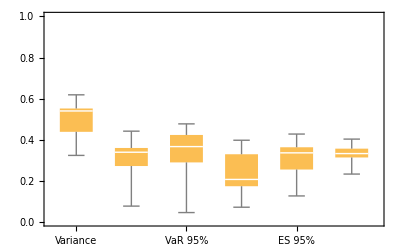

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
DateString[dates⟦1⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}]
```

2020-07-17-21-00-00

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day", "Hour", "Minute", "Second"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

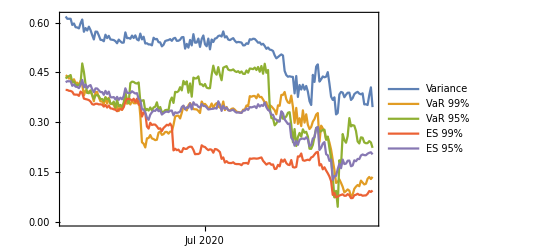

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

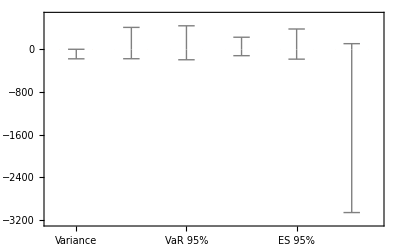

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day", "Hour", "Minute", "Second"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

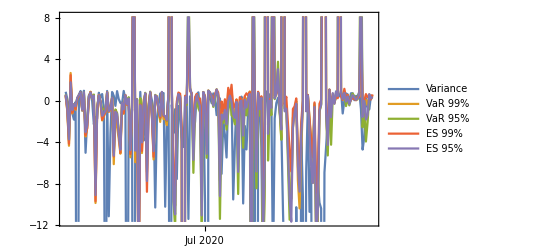

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

```mathematica
data[[1,5]]
```

rs

```mathematica
data[[1,6]]
```

rf

```mathematica
data[[2,2]]
```

2020-07-17 21:00:00

### In-sample P&L

```mathematica
dates[[1]]
```

{2020,6,17,1,0,0.}

```mathematica
data[[2,2]]
```

2020-07-17 21:00:00

```mathematica
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];
```

```mathematica
For[kk=0, kk≤185, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,5⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day", "Hour", "Minute", "Second"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day", "Hour", "Minute", "Second"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

```mathematica
data[[1;;10]]
```

( | datetime | spot | futures | rs | rf
0 | 2020-07-17 21:00:00 | 232.46 | 9241.75 | -0.00257776 | -0.000378644
1 | 2020-07-17 22:00:00 | 232.7 | 9232.75 | 0.0010319 | -0.000974316
2 | 2020-07-17 23:00:00 | 232.96 | 9237.25 | 0.00111669 | 0.000487277
3 | 2020-07-18 00:00:00 | 232.69 | 9241.75 | -0.00115967 | 0.000487039
4 | 2020-07-18 01:00:00 | 232.66 | 9233.75 | -0.000128935 | -0.000866012
5 | 2020-07-18 02:00:00 | 232.57 | 9228.25 | -0.000386905 | -0.000595818
6 | 2020-07-18 03:00:00 | 232.99 | 9227.75 | 0.00180428 | -0.0000541829
7 | 2020-07-18 04:00:00 | 233.03 | 9227.75 | 0.000171666 | 0.
8 | 2020-07-18 05:00:00 | 233.2 | 9231.75 | 0.000729254 | 0.000433381)

```mathematica
hvec
```

{{2020-07-17-21-00-00},{0.896771},{0.593447},{0.830416},{0.402843},{0.713809},{1.25838},{{0.015605253227364377, {h$428181854 -> 0.5934472895310408}},{0.00806645318672329, {h$428181854 -> 0.8304162861276098}},{0.01847639038339242, {h$428181854 -> 0.4028433867006832}},{0.012682094934318386, {h$428181854 -> 0.7138090162539178}},{0.011003114631020798, {h$428181854 -> 1.258383915139606}}}}

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤185, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,5⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

21.9.2022, BTC hourly: I stopped here as there is some issue with the date format, but the stuff below is not needed for the paper revision anyway.

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤185, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,5⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk<=185, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,5⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day","-", "Hour", "-", "Minute", "-", "Second"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day","-", "Hour", "-", "Minute", "-", "Second"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤185, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

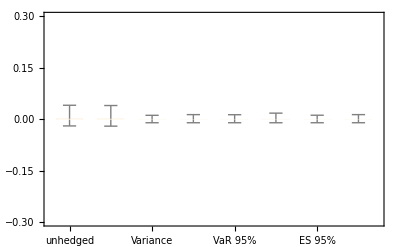

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

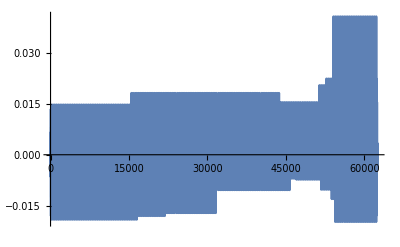

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤185, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

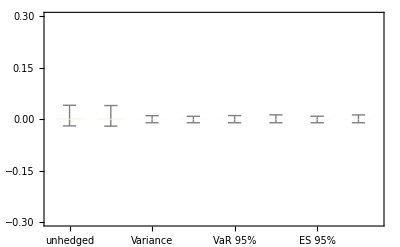

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
d[[3,1]]
```

2020-07-01

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day", "Hour", "Minute", "Second"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

DateString::str: String 2020-07-01 cannot be interpreted as a date in format {Year,Month,Day,Hour,Minute,Second}.

General::stop: Further output of DateString::str will be suppressed during this calculation.

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {{DateList[{2020-07-01,{Year,Month,Day,Hour,Minute,Second}}],0.000271636},{DateList[{2020-07-01,{Year,Month,Day,Hour,Minute,Second}}],0.00152253},«7»,{DateList[{2020-07-01,{Year,Month,Day,Hour,Minute,Second}}],-0.00159699},«734»} is not a valid dataset or list of datasets.

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {{DateList[{2020-07-01,{Year,Month,Day,Hour,Minute,Second}}],0.000151062},{DateList[{2020-07-01,{Year,Month,Day,Hour,Minute,Second}}],0.00124877},«7»,{DateList[{2020-07-01,{Year,Month,Day,Hour,Minute,Second}}],-0.00167852},«734»} is not a valid dataset or list of datasets.

{DateListPlot[(1),PlotRange→{-0.25,0.25}],DateListPlot[(1),PlotRange→{-0.25,0.25}]}
 |  |  |  |

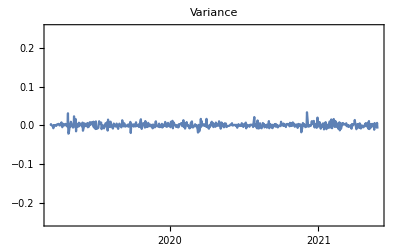
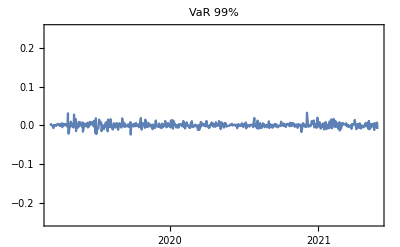
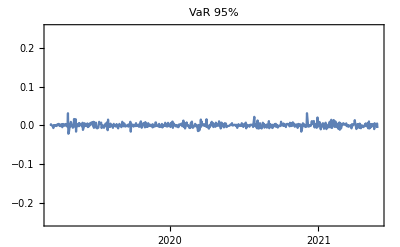
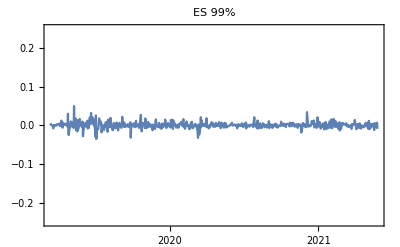
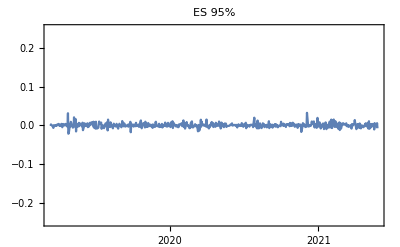
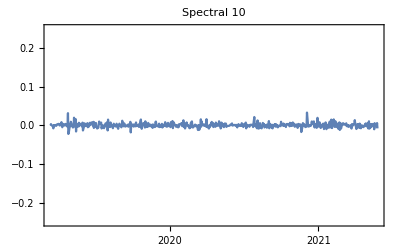

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

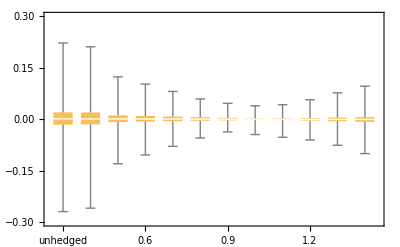

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

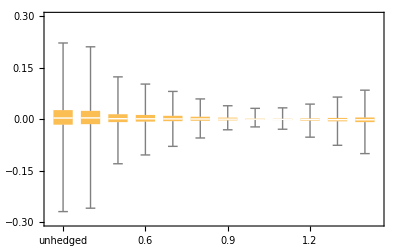

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤111, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-20 | 0.944958 | 0.936403 | 0.960422 | 0.939858 | 0.95253 | 0.949929
2021-05-13 | 0.944997 | 0.939292 | 0.95798 | 0.939858 | 0.950929 | 0.955053
2021-05-06 | 0.944795 | 0.939567 | 0.957988 | 0.939858 | 0.950902 | 0.955056
2021-04-29 | 0.945655 | 0.939858 | 0.957783 | 0.939858 | 0.951419 | 0.953189
2021-04-22 | 0.945022 | 0.939858 | 0.956836 | 0.939858 | 0.951895 | 0.95783
2021-04-15 | 0.943477 | 0.939858 | 0.957584 | 0.939858 | 0.950425 | 0.956884
2021-04-08 | 0.943478 | 0.939858 | 0.957346 | 0.939858 | 0.950425 | 0.957729
2021-04-01 | 0.944295 | 0.939858 | 0.957436 | 0.939858 | 0.950425 | 0.960253
2021-03-25 | 0.944517 | 0.939858 | 0.957748 | 0.939858 | 0.950425 | 0.957551
2021-03-18 | 0.944912 | 0.939858 | 0.958286 | 0.939858 | 0.950425 | 0.951931
2021-03-11 | 0.944109 | 0.939858 | 0.95762 | 0.939858 | 0.950425 | 0.949216
2021-03-04 | 0.9438 | 0.939858 | 0.957367 | 0.939858 | 0.950425 | 0.951002
2021-02-25 | 0.942553 | 0.939858 | 0.957789 | 0.939858 | 0.950686 | 0.951244
2021-02-18 | 0.943591 | 0.939858 | 0.957953 | 0.939858 | 0.950722 | 0.952645
2021-02-10 | 0.943575 | 0.939858 | 0.957789 | 0.939858 | 0.950686 | 0.951534
2021-02-03 | 0.942488 | 0.939858 | 0.957548 | 0.939858 | 0.950425 | 0.948618
2021-01-27 | 0.943994 | 0.939858 | 0.957388 | 0.939858 | 0.950425 | 0.951436
2021-01-20 | 0.943575 | 0.933217 | 0.957789 | 0.939858 | 0.950425 | 0.94659
2021-01-12 | 0.942291 | 0.939858 | 0.958821 | 0.939858 | 0.950425 | 0.951074
2021-01-05 | 0.937763 | 0.939858 | 0.926461 | 0.939858 | 0.941973 | 0.950224
2020-12-28 | 0.939688 | 0.942848 | 0.935498 | 0.931769 | 0.950043 | 0.948606
2020-12-18 | 0.938988 | 0.930508 | 0.940857 | 0.930508 | 0.948615 | 0.948099
2020-12-11 | 0.937418 | 0.930508 | 0.93659 | 0.929982 | 0.948912 | 0.948502
2020-12-04 | 0.937351 | 0.930508 | 0.937615 | 0.930508 | 0.948485 | 0.945604
2020-11-27 | 0.940641 | 0.949384 | 0.958542 | 0.937226 | 0.951376 | 0.946668
2020-11-19 | 0.941777 | 0.948722 | 0.958542 | 0.935753 | 0.951305 | 0.948856
2020-11-12 | 0.942044 | 0.96104 | 0.940723 | 0.953136 | 0.953458 | 0.943633
2020-11-05 | 0.940802 | 0.942962 | 0.934453 | 0.927417 | 0.950425 | 0.939673
2020-10-29 | 0.94099 | 0.96104 | 0.937759 | 0.952019 | 0.951658 | 0.943262
2020-10-22 | 0.940562 | 0.939867 | 0.93415 | 0.926782 | 0.950425 | 0.940401
2020-10-15 | 0.938923 | 0.938557 | 0.93375 | 0.926837 | 0.950425 | 0.940648
2020-10-08 | 0.939694 | 0.942708 | 0.933299 | 0.928603 | 0.950344 | 0.941757
2020-10-01 | 0.937485 | 0.924236 | 0.929361 | 0.922275 | 0.949601 | 0.939241
2020-09-24 | 0.937893 | 0.926261 | 0.924532 | 0.923896 | 0.950097 | 0.942868
2020-09-17 | 0.938604 | 0.943226 | 0.929538 | 0.923896 | 0.949641 | 0.944185
2020-09-10 | 0.938103 | 0.928079 | 0.929361 | 0.924417 | 0.949641 | 0.939386
2020-09-02 | 0.946997 | 0.96261 | 0.952165 | 0.959915 | 0.969274 | 0.938439
2020-08-26 | 0.951508 | 0.974346 | 0.95186 | 0.957458 | 0.968364 | 0.948049
2020-08-19 | 0.952679 | 0.968305 | 0.934266 | 0.966517 | 0.969688 | 0.948099
2020-08-12 | 0.952895 | 0.967749 | 0.934488 | 0.966633 | 0.969688 | 0.948492
2020-08-05 | 0.95096 | 0.941415 | 0.946592 | 0.95572 | 0.961297 | 0.945351
2020-07-29 | 0.952553 | 0.973319 | 0.952524 | 0.957899 | 0.968558 | 0.950066
2020-07-22 | 0.955108 | 0.973169 | 0.950411 | 0.958416 | 0.968558 | 0.954573
2020-07-15 | 0.953608 | 0.958604 | 0.956209 | 0.952615 | 0.967411 | 0.962158
2020-07-08 | 0.954 | 0.960096 | 0.957235 | 0.953315 | 0.967629 | 0.952328
2020-06-30 | 0.948643 | 0.938719 | 0.948944 | 0.935451 | 0.964035 | 0.946958
2020-06-23 | 0.948852 | 0.937191 | 0.948944 | 0.935109 | 0.964034 | 0.947431
2020-06-16 | 0.949394 | 0.93732 | 0.948944 | 0.935916 | 0.964202 | 0.947068
2020-06-09 | 0.950762 | 0.928101 | 0.944033 | 0.926849 | 0.963285 | 0.965948
2020-06-02 | 0.950521 | 0.931507 | 0.943374 | 0.927556 | 0.96335 | 0.965397
2020-05-26 | 0.950143 | 0.985633 | 0.946615 | 0.924463 | 0.961017 | 0.964796
2020-05-18 | 0.949726 | 0.973912 | 0.946639 | 0.923013 | 0.961372 | 0.964141
2020-05-11 | 0.949043 | 0.924443 | 0.942083 | 0.922073 | 0.961265 | 0.962554
2020-05-04 | 0.948231 | 0.939595 | 0.952671 | 0.957876 | 0.952671 | 0.953638
2020-04-27 | 0.948305 | 0.943333 | 0.948617 | 0.965464 | 0.953125 | 0.94799
2020-04-20 | 0.947418 | 0.932229 | 0.951637 | 0.967081 | 0.956018 | 0.948411
2020-04-13 | 0.946247 | 0.974895 | 0.94906 | 0.963845 | 0.950352 | 0.948831
2020-04-03 | 0.946647 | 0.972179 | 0.948412 | 0.962009 | 0.956572 | 0.953347
2020-03-27 | 0.946869 | 1.00313 | 0.957267 | 0.931201 | 0.965361 | 0.955997
2020-03-20 | 0.948047 | 0.932019 | 0.945609 | 0.927565 | 0.961887 | 0.954419
2020-03-13 | 0.940912 | 0.990325 | 0.951484 | 0.915055 | 0.954039 | 0.948019
2020-03-06 | 0.952808 | 0.981084 | 0.969034 | 0.894546 | 0.966617 | 0.981311
2020-02-28 | 0.951281 | 0.974535 | 0.928525 | 0.92524 | 0.949669 | 0.972828
2020-02-21 | 0.945766 | 0.96834 | 0.929343 | 0.912902 | 0.947423 | 0.944412
2020-02-13 | 0.947609 | 0.972418 | 0.96335 | 0.907758 | 0.954059 | 0.954091
2020-02-06 | 0.949967 | 0.968464 | 0.969217 | 0.910579 | 0.947851 | 0.970498
2020-01-30 | 0.945028 | 0.987854 | 0.964551 | 0.894115 | 0.956116 | 0.950736
2020-01-23 | 0.945315 | 0.991206 | 0.973714 | 0.889839 | 0.962378 | 0.951877
2020-01-15 | 0.943978 | 0.895572 | 0.975917 | 0.890487 | 0.97419 | 0.956251
2020-01-08 | 0.942792 | 0.888685 | 0.981181 | 0.884826 | 0.965118 | 0.936911
2019-12-31 | 0.942787 | 0.903469 | 0.979171 | 0.883563 | 0.964381 | 0.954428
2019-12-23 | 0.937528 | 0.905962 | 0.962848 | 0.858632 | 0.958957 | 0.942796
2019-12-16 | 0.940426 | 0.906818 | 0.965785 | 0.862065 | 0.960032 | 0.948748
2019-12-09 | 0.940839 | 0.896899 | 0.965173 | 0.862906 | 0.960506 | 0.947723
2019-12-02 | 0.940577 | 0.928648 | 0.964508 | 0.859172 | 0.955141 | 0.94551
2019-11-22 | 0.941498 | 0.908013 | 0.984811 | 0.862425 | 0.960168 | 0.95208
2019-11-15 | 0.939936 | 0.90337 | 0.978352 | 0.85984 | 0.958581 | 0.95817
2019-11-08 | 0.941661 | 0.907919 | 0.985419 | 0.86262 | 0.960159 | 0.952459
2019-11-01 | 0.941527 | 0.929728 | 0.967677 | 0.859583 | 0.955072 | 0.948766
2019-10-25 | 0.942203 | 0.900304 | 0.973538 | 0.865457 | 0.961747 | 0.950274
2019-10-18 | 0.942618 | 0.921892 | 0.977259 | 0.867404 | 0.962414 | 0.946753
2019-10-11 | 0.943893 | 0.922422 | 0.966945 | 0.863127 | 0.960883 | 0.952272
2019-10-04 | 0.944615 | 0.976721 | 0.989154 | 0.87093 | 0.971163 | 0.954409
2019-09-27 | 0.945315 | 0.907969 | 0.978127 | 0.867928 | 0.964172 | 0.954875
2019-09-20 | 0.94772 | 0.918224 | 0.971904 | 0.862493 | 0.961773 | 0.958886
2019-09-13 | 0.94814 | 0.91219 | 0.976634 | 0.867404 | 0.962962 | 0.955369
2019-09-06 | 0.949256 | 0.900032 | 0.966959 | 0.86491 | 0.961401 | 0.963012
2019-08-29 | 0.948447 | 0.905568 | 0.983225 | 0.86835 | 0.967502 | 0.960036
2019-08-22 | 0.949349 | 0.897549 | 0.9765 | 0.866493 | 0.962111 | 0.953764
2019-08-15 | 0.949441 | 0.902986 | 0.982439 | 0.867701 | 0.967015 | 0.959643
2019-08-08 | 0.950159 | 0.897288 | 0.988252 | 0.865484 | 0.963519 | 0.969646
2019-08-01 | 0.950575 | 0.898312 | 0.990852 | 0.869066 | 0.963959 | 0.967383
2019-07-25 | 0.952708 | 0.904081 | 0.977705 | 0.873133 | 0.963862 | 0.962677
2019-07-18 | 0.954122 | 0.912066 | 0.986841 | 0.872194 | 0.964292 | 0.963211
2019-07-11 | 0.954632 | 0.904948 | 0.981671 | 0.877109 | 0.962495 | 0.970682
2019-07-03 | 0.955577 | 0.909995 | 0.971198 | 0.877107 | 0.963871 | 0.963649
2019-06-26 | 0.952699 | 0.890509 | 0.977367 | 0.83414 | 0.959233 | 0.983879
2019-06-19 | 0.948754 | 0.94835 | 0.955752 | 0.823502 | 0.950703 | 0.959149
2019-06-12 | 0.949835 | 0.940703 | 0.976824 | 0.831524 | 0.963893 | 0.963056
2019-06-05 | 0.952382 | 0.936468 | 0.973488 | 0.829031 | 0.967053 | 0.959272
2019-05-29 | 0.953816 | 0.9319 | 0.973078 | 0.828212 | 0.966652 | 0.960235
2019-05-21 | 0.952927 | 0.910769 | 0.960888 | 0.817208 | 0.952976 | 0.961782
2019-05-14 | 0.954353 | 0.925084 | 0.97557 | 0.824959 | 0.960902 | 0.957063
2019-05-07 | 0.958395 | 0.938385 | 0.988898 | 0.842331 | 0.969916 | 0.974121
2019-04-30 | 0.959189 | 0.931491 | 0.989477 | 0.853378 | 0.973908 | 0.958102
2019-04-23 | 0.968071 | 0.960433 | 0.976322 | 0.889152 | 0.973911 | 0.987324
2019-04-15 | 0.968985 | 0.966333 | 0.990623 | 0.899854 | 0.973283 | 0.97487
2019-04-08 | 0.968988 | 0.953813 | 0.982515 | 0.885351 | 0.982884 | 0.978232
2019-04-01 | 0.967466 | 0.983798 | 0.997575 | 0.937425 | 0.992702 | 0.963878
2019-03-25 | 0.975057 | 0.964903 | 1.06264 | 0.954191 | 1.02416 | 0.971195
2019-03-18 | 0.974561 | 0.996531 | 0.998379 | 0.952044 | 1.0254 | 0.95721
2019-03-11 | 0.975732 | 0.957384 | 0.999247 | 0.960651 | 1.03466 | 0.971906)

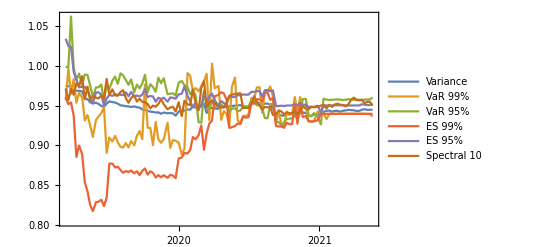

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods,PlotRange->Full]
```